# Ejecuciones del brutal para la tesis

```mathematica
Needs["Quantum`"]
Needs["Carlos`"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates"]
```

/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates

## Funciones útiles

```mathematica
ItppVectorToExpression[vector_String] := 
 ToExpression /@ 
  StringSplit[
   StringReplace[
    StringTake[vector, {2, -2}], {"i" -> "I", "e+" :> "*^", 
     "e-" :> "*^-"}]]
```

```mathematica
brutalSampleCPP[swapP_, ϵ_, N_, rz_]:= ItppVectorToExpression /@ (RAW = 
     ReadListUncomment[
      "!/media/storage/ciencia/investigacion/proyecto-ss/adanerick/codigo/cg -o get_states_bruto -s 0 --swap_probability " <> 
       ToString[swapP] <> " --max_tolerance " <> 
       ToString[ϵ] <> " --sample_size " <> 
       ToString[N] <> " --r_z " <> ToString[rz], String]);
```

## Ejecuciones del algoritmo

### Ejecución para rz = 0

```mathematica
sampleSize = 10000;
rz = 0;
MaxError = 0.01;
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
brutalsRcero = MapMonitored[ItppVectorToExpression /@ (RAW = 
     ReadListUncomment[
      "!/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/cg -o get_states_bruto -s 0 --swap_probability " <> 
       ToString[#] <> " --max_tolerance " <> 
       ToString[MaxError] <> " --sample_size " <> 
       ToString[sampleSize] <> " --r_z " <> ToString[0], String])&, swapPs];
brutalsRptoCinco = MapMonitored[ItppVectorToExpression /@ (RAW = 
     ReadListUncomment[
      "!/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/cg -o get_states_bruto -s 0 --swap_probability " <> 
       ToString[#] <> " --max_tolerance " <> 
       ToString[MaxError] <> " --sample_size " <> 
       ToString[sampleSize] <> " --r_z " <> ToString[0.5], String])&, swapPs];
brutalsRptoOcho = MapMonitored[ItppVectorToExpression /@ (RAW = 
     ReadListUncomment[
      "!/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/cg -o get_states_bruto -s 0 --swap_probability " <> 
       ToString[#] <> " --max_tolerance " <> 
       ToString[MaxError] <> " --sample_size " <> 
       ToString[sampleSize] <> " --r_z " <> ToString[0.8], String])&, swapPs];
```

```mathematica
Export["brutalSamples3_rz=0.8_N=10000_eps=0.01_allswapPs.m", brutalsRptoOcho]
```

brutalSamples3_rz=0.8_N=10000_eps=0.01_allswapPs.m

### Ejecución para rz = 0.5

```mathematica
sampleSize = 7000;
rz = 0.5;
MaxError = 0.01;
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
rz
```

0.5

```mathematica
brutalsRptoCinco = MapMonitored[ItppVectorToExpression /@ (RAW = 
     ReadListUncomment[
      "!/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/cg -o get_states_bruto -s 0 --swap_probability " <> 
       ToString[#] <> " --max_tolerance " <> 
       ToString[MaxError] <> " --sample_size " <> 
       ToString[sampleSize] <> " --r_z " <> ToString[rz], String])&, swapPs];
```

```mathematica
Export["brutalSamples2_rz=0.5_N=7000_eps=0.01_allswapPs.m", brutalsRptoCinco]
```

brutalSamples2_rz=0.5_N=7000_eps=0.01_allswapPs.m

### Ejecución para rz = 0.8

```mathematica
sampleSize = 5000;
rz = 0.8;
MaxError = 0.01;
swapP = 0.8;
```

```mathematica
Directory[]
```

/media/storage/ciencia/investigacion/tesis/muestras_brutales_extra/samplesRp8Pp8

```mathematica
Do[
	sample = Timing[brutalSampleCPP[swapP, MaxError, sampleSize, rz]];
	Export["brutalSample_N=5000_err=0.01_rz=0.8_p=0.8_"<>ToString[i]<>".wl", sample];
	Print["guardada la muestra rz=0.8, p=0.8 numero: "<>ToString[i]]
,{i, 31, 40}]
```

guardada la muestra rz=0.8, p=0.8 numero: 31

guardada la muestra rz=0.8, p=0.8 numero: 32

guardada la muestra rz=0.8, p=0.8 numero: 33

guardada la muestra rz=0.8, p=0.8 numero: 34

guardada la muestra rz=0.8, p=0.8 numero: 35

guardada la muestra rz=0.8, p=0.8 numero: 36

guardada la muestra rz=0.8, p=0.8 numero: 37

guardada la muestra rz=0.8, p=0.8 numero: 38

$Aborted

## Cálculo de los estados promedio

```mathematica
(*Cargar datos de las muestras:*)
(*r_z = 0, p = 0.3*)
preim1 = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"];
(*r_z = 0, p = 0.5*)
preim2 = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"];
(*r_z = 0.5, p = 0.3*)
preim3 = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"];
(*r_z = 0.5, p = 0.5*)
preim4 = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"];
(*r_z = 0.5, p = 0.8*)
preim5 = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"];
```

```mathematica
(*Convertir datos a matrices de densidad*)
allPreimages = ketsToDensity /@ {preim1, preim2, preim3, preim4, preim5};
```

```mathematica
(*visualizacion *)
visualizeBipartiteSystemWObj[allPreimages[[3]], {{0.75, 0}, {0, 0.25}}]
```

-Graphics3D-

```mathematica
Export["full_ergodic_sphere.pdf", %17]
```

full_ergodic_sphere.pdf

```mathematica
Clear[preim1, preim2, preim3, preim4, preim5]
```

```mathematica
Dimensions@allPreimages
```

{5,10000,4,4}

```mathematica
averageStates = preimageMean[#]& /@ allPreimages;
```

```mathematica
averageStates//Dimensions
```

{5}

```mathematica
MatrixForm /@ averageStates
```

{(0.211193+0. ⅈ | 0.00226188+0.000322871 ⅈ | -0.0000387278-0.00218999 ⅈ | 0.00161537+0.000847337 ⅈ
0.00226188-0.000322871 ⅈ | 0.288714+0. ⅈ | -0.0695457+0.000643935 ⅈ | -0.0000533045+0.00230781 ⅈ
-0.0000387278+0.00218999 ⅈ | -0.0695457-0.000643935 ⅈ | 0.288848+0. ⅈ | -0.00218745-0.000486151 ⅈ
0.00161537-0.000847337 ⅈ | -0.0000533045-0.00230781 ⅈ | -0.00218745+0.000486151 ⅈ | 0.211245+0. ⅈ),(0.16773+0. ⅈ | 0.00356867+0.00108112 ⅈ | -0.00134209-0.000906195 ⅈ | -0.00191551-0.0017498 ⅈ
0.00356867-0.00108112 ⅈ | 0.332799+0. ⅈ | -0.167539+0.000400689 ⅈ | 0.0000163545-0.000791055 ⅈ
-0.00134209+0.000906195 ⅈ | -0.167539-0.000400689 ⅈ | 0.331714+0. ⅈ | -0.00217105+0.000626583 ⅈ
-0.00191551+0.0017498 ⅈ | 0.0000163545+0.000791055 ⅈ | -0.00217105-0.000626583 ⅈ | 0.167758+0. ⅈ),(0.473305+0. ⅈ | 0.000655606+2.84531×10^-6 ⅈ | -0.000318089-0.0015224 ⅈ | 0.00331696-0.00145357 ⅈ
0.000655606-2.84531×10^-6 ⅈ | 0.0542507+0. ⅈ | -0.0868121-0.000578989 ⅈ | 0.0000924854+0.000310191 ⅈ
-0.000318089+0.0015224 ⅈ | -0.0868121+0.000578989 ⅈ | 0.371936+0. ⅈ | -0.000540418+0.000498622 ⅈ
0.00331696+0.00145357 ⅈ | 0.0000924854-0.000310191 ⅈ | -0.000540418-0.000498622 ⅈ | 0.100508+0. ⅈ),(0.62448+0. ⅈ | 0.0024765-0.00374858 ⅈ | -0.00260154+0.00379765 ⅈ | 0.00192298-0.00275803 ⅈ
0.0024765+0.00374858 ⅈ | 0.125419+0. ⅈ | -0.125318+0.0000369971 ⅈ | 0.000768097-0.000025098 ⅈ
-0.00260154-0.00379765 ⅈ | -0.125318-0.0000369971 ⅈ | 0.125453+0. ⅈ | -0.000735714+0.000016436 ⅈ
0.00192298+0.00275803 ⅈ | 0.000768097+0.000025098 ⅈ | -0.000735714-0.000016436 ⅈ | 0.124647+0. ⅈ),(0.3669+0. ⅈ | 0.00242533+0.00505976 ⅈ | 0.00114443-0.00131128 ⅈ | 0.000871117-0.000535486 ⅈ
0.00242533-0.00505976 ⅈ | 0.459019+0. ⅈ | -0.0408446+0.000400721 ⅈ | -0.00168835+0.000371534 ⅈ
0.00114443+0.00131128 ⅈ | -0.0408446-0.000400721 ⅈ | 0.0793262+0. ⅈ | -0.000367446-0.00105785 ⅈ
0.000871117+0.000535486 ⅈ | -0.00168835-0.000371534 ⅈ | -0.000367446+0.00105785 ⅈ | 0.0947549+0. ⅈ)}

```mathematica
averageStatesRound = numForm[#, 4]& /@ averageStates;
MatrixForm /@ Chop[averageStatesRound]
```

{(0.2112 | 0.002262+0.0003229 ⅈ | -0.00003873-0.00219 ⅈ | 0.001615+0.0008473 ⅈ
0.002262-0.0003229 ⅈ | 0.2887 | -0.06955+0.0006439 ⅈ | -0.0000533+0.002308 ⅈ
-0.00003873+0.00219 ⅈ | -0.06955-0.0006439 ⅈ | 0.2888 | -0.002187-0.0004862 ⅈ
0.001615-0.0008473 ⅈ | -0.0000533-0.002308 ⅈ | -0.002187+0.0004862 ⅈ | 0.2112),(0.1677 | 0.003569+0.001081 ⅈ | -0.001342-0.0009062 ⅈ | -0.001916-0.00175 ⅈ
0.003569-0.001081 ⅈ | 0.3328 | -0.1675+0.0004007 ⅈ | 0.00001635-0.0007911 ⅈ
-0.001342+0.0009062 ⅈ | -0.1675-0.0004007 ⅈ | 0.3317 | -0.002171+0.0006266 ⅈ
-0.001916+0.00175 ⅈ | 0.00001635+0.0007911 ⅈ | -0.002171-0.0006266 ⅈ | 0.1678),(0.4733 | 0.0006556+(2.845×10^-6) ⅈ | -0.0003181-0.001522 ⅈ | 0.003317-0.001454 ⅈ
0.0006556-(2.845×10^-6) ⅈ | 0.05425 | -0.08681-0.000579 ⅈ | 0.00009249+0.0003102 ⅈ
-0.0003181+0.001522 ⅈ | -0.08681+0.000579 ⅈ | 0.3719 | -0.0005404+0.0004986 ⅈ
0.003317+0.001454 ⅈ | 0.00009249-0.0003102 ⅈ | -0.0005404-0.0004986 ⅈ | 0.1005),(0.6245 | 0.002476-0.003749 ⅈ | -0.002602+0.003798 ⅈ | 0.001923-0.002758 ⅈ
0.002476+0.003749 ⅈ | 0.1254 | -0.1253+0.000037 ⅈ | 0.0007681-0.0000251 ⅈ
-0.002602-0.003798 ⅈ | -0.1253-0.000037 ⅈ | 0.1255 | -0.0007357+0.00001644 ⅈ
0.001923+0.002758 ⅈ | 0.0007681+0.0000251 ⅈ | -0.0007357-0.00001644 ⅈ | 0.1246),(0.3669 | 0.002425+0.00506 ⅈ | 0.001144-0.001311 ⅈ | 0.0008711-0.0005355 ⅈ
0.002425-0.00506 ⅈ | 0.459 | -0.04084+0.0004007 ⅈ | -0.001688+0.0003715 ⅈ
0.001144+0.001311 ⅈ | -0.04084-0.0004007 ⅈ | 0.07933 | -0.0003674-0.001058 ⅈ
0.0008711+0.0005355 ⅈ | -0.001688-0.0003715 ⅈ | -0.0003674+0.001058 ⅈ | 0.09475)}

```mathematica
matrixLatexStrings = MatrixToLatex2[#]& /@ averageStatesRound;
```

```mathematica
Print[#<>"\n"]& /@ matrixLatexStrings
```

\begin{pmatrix}
0.21 + 0. i&0.0023 + 0.00032 i&-0.000039 - 0.0022 i&0.0016 + 0.00085 i\\0.0023 - 0.00032 i&0.29 + 0. i&-0.07 + 0.00064 i&-0.000053 + 0.0023 i\\-0.000039 + 0.0022 i&-0.07 - 0.00064 i&0.29 + 0. i&-0.0022 - 0.00049 i\\0.0016 - 0.00085 i&-0.000053 - 0.0023 i&-0.0022 + 0.00049 i&0.21 + 0. i
\end{pmatrix}

\begin{pmatrix}
0.17 + 0. i&0.0036 + 0.0011 i&-0.0013 - 0.00091 i&-0.0019 - 0.0017 i\\0.0036 - 0.0011 i&0.33 + 0. i&-0.17 + 0.0004 i&0.000016 - 0.00079 i\\-0.0013 + 0.00091 i&-0.17 - 0.0004 i&0.33 + 0. i&-0.0022 + 0.00063 i\\-0.0019 + 0.0017 i&0.000016 + 0.00079 i&-0.0022 - 0.00063 i&0.17 + 0. i
\end{pmatrix}

\begin{pmatrix}
0.47 + 0. i&                  -6
0.00066 + 2.8 × 10   i&-0.00032 - 0.0015 i&0.0033 - 0.0015 i\\                  -6
0.00066 - 2.8 × 10   i&0.054 + 0. i&-0.087 - 0.00058 i&0.000092 + 0.00031 i\\-0.00032 + 0.0015 i&-0.087 + 0.00058 i&0.37 + 0. i&-0.00054 + 0.0005 i\\0.0033 + 0.0015 i&0.000092 - 0.00031 i&-0.00054 - 0.0005 i&0.1 + 0. i
\end{pmatrix}

\begin{pmatrix}
0.62 + 0. i&0.0025 - 0.0037 i&-0.0026 + 0.0038 i&0.0019 - 0.0028 i\\0.0025 + 0.0037 i&0.13 + 0. i&-0.13 + 0.000037 i&0.00077 - 0.000025 i\\-0.0026 - 0.0038 i&-0.13 - 0.000037 i&0.13 + 0. i&-0.00074 + 0.000016 i\\0.0019 + 0.0028 i&0.00077 + 0.000025 i&-0.00074 - 0.000016 i&0.12 + 0. i
\end{pmatrix}

\begin{pmatrix}
0.37 + 0. i&0.0024 + 0.0051 i&0.0011 - 0.0013 i&0.00087 - 0.00054 i\\0.0024 - 0.0051 i&0.46 + 0. i&-0.041 + 0.0004 i&-0.0017 + 0.00037 i\\0.0011 + 0.0013 i&-0.041 - 0.0004 i&0.079 + 0. i&-0.00037 - 0.0011 i\\0.00087 + 0.00054 i&-0.0017 - 0.00037 i&-0.00037 + 0.0011 i&0.095 + 0. i
\end{pmatrix}

```mathematica
Max[Norm[# - (IdentityMatrix[2]/2),"Frobenius"]& /@ (coarseGraining2[#, 0.3]& /@ allPreimages[[1]])]
```

0.00999931

```mathematica
Max[Norm[# - (IdentityMatrix[2]/2),"Frobenius"]& /@ (coarseGraining2[#, 0.5]& /@ allPreimages[[2]])]
```

0.00999891

```mathematica
Max[Norm[# - (IdentityMatrix[2]/2 + PauliMatrix[3]/4),"Frobenius"]& /@ (coarseGraining2[#, 0.3]& /@ allPreimages[[3]])]
```

0.00999982

```mathematica
Max[Norm[# - (IdentityMatrix[2]/2 + PauliMatrix[3]/4),"Frobenius"]& /@ (coarseGraining2[#, 0.5]& /@ allPreimages[[4]])]
```

0.00999997

```mathematica
Max[Norm[# - (IdentityMatrix[2]/2 + PauliMatrix[3]/4),"Frobenius"]& /@ (coarseGraining2[#, 0.8]& /@ allPreimages[[5]])]
```

0.00999983

### Cálculos de los estados promedio para r_z = 0.8

```mathematica
(*Pa cuando no se ejecuta, sino que sólo se importan los datos:*)
pimCeroPuntoTresKets = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"];
pimCeroPuntoCincoKets = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"];
pimCeroPuntoOchoKets = Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"];
```

```mathematica
(*Convertimos primero a matrices de densidad:*)
(*pimCeroPuntoTres = ketsToDensity[brutalStatesCeroPuntoOcho[[1]]];
pimCeroPuntoCinco = ketsToDensity[brutalStatesCeroPuntoOcho[[2]]];
pimCeroPuntoOcho = ketsToDensity[brutalStatesCeroPuntoOcho[[3]]];*)
(*Pa cuando los datos son importados:*)
pimCeroPuntoTres = ketsToDensity[pimCeroPuntoTresKets];
pimCeroPuntoCinco = ketsToDensity[pimCeroPuntoCincoKets];
pimCeroPuntoOcho = ketsToDensity[pimCeroPuntoOchoKets];
```

```mathematica
targetCeroPuntoOcho = 0.5 IdentityMatrix[2] + 0.4 PauliMatrix[3];
```

#### Resultados para p = 0.3

```mathematica
(*visualizaciones*)
rPuntoOchopPuntoTresVis1 = visualizeBipartiteSystemWObj[pimCeroPuntoTres[[1;;100]], targetCeroPuntoOcho];
rPuntoOchopPuntoTresVis2 = visualizeBipartiteSystemWObj[pimCeroPuntoTres[[1;;1000]], targetCeroPuntoOcho];
rPuntoOchopPuntoTresVis3 = visualizeBipartiteSystemWObj[pimCeroPuntoTres, targetCeroPuntoOcho];
```

```mathematica
Export["brutalRES_n=100_p=0.3_rz=0.8.png", rPuntoOchopPuntoTresVis1]
Export["brutalRES_n=1000_p=0.3_rz=0.8.png", rPuntoOchopPuntoTresVis2]
Export["brutalRES_n=10000_p=0.3_rz=0.8.png",rPuntoOchopPuntoTresVis3]
```

brutalRES_n=100_p=0.3_rz=0.8.png

brutalRES_n=1000_p=0.3_rz=0.8.png

brutalRES_n=10000_p=0.3_rz=0.8.png

```mathematica
Grid[{{rPuntoOchopPuntoTresVis1, rPuntoOchopPuntoTresVis2, rPuntoOchopPuntoTresVis3}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(*Estado promedio*)
avgStateCeroPuntoTres = preimageMean[pimCeroPuntoTres];
avgStateCeroPuntoTresRound = numForm[avgStateCeroPuntoTres, 2];
avgStateCeroPuntoTresRound//MatrixForm
```

(0.81+0. ⅈ | -0.00024+0.00094 ⅈ | 0.00098-0.00093 ⅈ | 0.00026-0.00063 ⅈ
-0.00024-0.00094 ⅈ | 0.021+0. ⅈ | -0.047-(6.7×10^-6) ⅈ | 0.00012+0.00026 ⅈ
0.00098+0.00093 ⅈ | -0.047+(6.7×10^-6) ⅈ | 0.12+0. ⅈ | -0.00022-0.00059 ⅈ
0.00026+0.00063 ⅈ | 0.00012-0.00026 ⅈ | -0.00022+0.00059 ⅈ | 0.048+0. ⅈ)

```mathematica
(*Conversión a latex*)
MatrixToLatex2[avgStateCeroPuntoTresRound]
```

\begin{pmatrix}
0.81 + 0. i&-0.00024 + 0.00094 i&0.00098 - 0.00093 i&0.00026 - 0.00063 i\\-0.00024 - 0.00094 i&0.021 + 0. i&                 -6
-0.047 - 6.7 × 10   i&0.00012 + 0.00026 i\\0.00098 + 0.00093 i&                 -6
-0.047 + 6.7 × 10   i&0.12 + 0. i&-0.00022 - 0.00059 i\\0.00026 + 0.00063 i&0.00012 - 0.00026 i&-0.00022 + 0.00059 i&0.048 + 0. i
\end{pmatrix}

#### Resultados para p = 0.5

```mathematica
(*visualizaciones*)
rPuntoOchopPuntoCincoVis1 = visualizeBipartiteSystemWObj[pimCeroPuntoCinco[[1;;100]], targetCeroPuntoOcho];
rPuntoOchopPuntoCincoVis2 = visualizeBipartiteSystemWObj[pimCeroPuntoCinco[[1;;1000]], targetCeroPuntoOcho];
rPuntoOchopPuntoCincoVis3 = visualizeBipartiteSystemWObj[pimCeroPuntoCinco, targetCeroPuntoOcho];
```

```mathematica
Export["brutalRES_n=100_p=0.5_rz=0.8.png", rPuntoOchopPuntoCincoVis1]
Export["brutalRES_n=1000_p=0.5_rz=0.8.png", rPuntoOchopPuntoCincoVis2]
Export["brutalRES_n=10000_p=0.5_rz=0.8.png",rPuntoOchopPuntoCincoVis3]
```

brutalRES_n=100_p=0.5_rz=0.8.png

brutalRES_n=1000_p=0.5_rz=0.8.png

brutalRES_n=10000_p=0.5_rz=0.8.png

```mathematica
Grid[{{rPuntoOchopPuntoCincoVis1,rPuntoOchopPuntoCincoVis2, rPuntoOchopPuntoCincoVis3}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(*Estado promedio*)
avgStateCeroPuntoCinco = preimageMean[pimCeroPuntoCinco];
avgStateCeroPuntoCincoRound = numForm[avgStateCeroPuntoCinco, 2];
avgStateCeroPuntoCincoRound//MatrixForm
```

(0.85+0. ⅈ | 0.0019+0.00091 ⅈ | -0.0019-0.00096 ⅈ | -0.00038+0.0004 ⅈ
0.0019-0.00091 ⅈ | 0.05+0. ⅈ | -0.05-0.000014 ⅈ | -0.00017+0.0004 ⅈ
-0.0019+0.00096 ⅈ | -0.05+0.000014 ⅈ | 0.05+0. ⅈ | 0.00017-0.00042 ⅈ
-0.00038-0.0004 ⅈ | -0.00017-0.0004 ⅈ | 0.00017+0.00042 ⅈ | 0.05+0. ⅈ)

```mathematica
(*conversión a Latex*)
MatrixToLatex2[avgStateCeroPuntoCincoRound]
```

\begin{pmatrix}
0.85 + 0. i&0.0019 + 0.00091 i&-0.0019 - 0.00096 i&-0.00038 + 0.0004 i\\0.0019 - 0.00091 i&0.05 + 0. i&-0.05 - 0.000014 i&-0.00017 + 0.0004 i\\-0.0019 + 0.00096 i&-0.05 + 0.000014 i&0.05 + 0. i&0.00017 - 0.00042 i\\-0.00038 - 0.0004 i&-0.00017 - 0.0004 i&0.00017 + 0.00042 i&0.05 + 0. i
\end{pmatrix}

#### Resultados para p = 0.8

```mathematica
(*visualizaciones*)
rPuntoOchopPuntoOchoVis1 = visualizeBipartiteSystemWObj[pimCeroPuntoOcho[[1;;100]], targetCeroPuntoOcho];
rPuntoOchopPuntoOchoVis2 = visualizeBipartiteSystemWObj[pimCeroPuntoOcho[[1;;1000]], targetCeroPuntoOcho];
rPuntoOchopPuntoOchoVis3 = visualizeBipartiteSystemWObj[pimCeroPuntoOcho, targetCeroPuntoOcho];
```

```mathematica
Export["brutalRES_n=100_p=0.8_rz=0.8.png", rPuntoOchopPuntoOchoVis1]
Export["brutalRES_n=1000_p=0.8_rz=0.8.png", rPuntoOchopPuntoOchoVis2]
Export["brutalRES_n=10000_p=0.8_rz=0.8.png",rPuntoOchopPuntoOchoVis3]
```

brutalRES_n=100_p=0.8_rz=0.8.png

brutalRES_n=1000_p=0.8_rz=0.8.png

brutalRES_n=10000_p=0.8_rz=0.8.png

```mathematica
Grid[{{rPuntoOchopPuntoOchoVis1, rPuntoOchopPuntoOchoVis2, rPuntoOchopPuntoOchoVis3}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(*Estado promedio*)
avgStateCeroPuntoOcho = preimageMean[pimCeroPuntoOcho];
avgStateCeroPuntoOchoRound = numForm[avgStateCeroPuntoOcho, 2];
avgStateCeroPuntoOchoRound//MatrixForm
```

(0.72+0. ⅈ | 0.0021-0.0016 ⅈ | -0.0007+0.000086 ⅈ | -0.00024-0.00047 ⅈ
0.0021+0.0016 ⅈ | 0.22+0. ⅈ | -0.04-0.00024 ⅈ | 0.00024+0.00033 ⅈ
-0.0007-0.000086 ⅈ | -0.04+0.00024 ⅈ | 0.015+0. ⅈ | -0.00014-0.000071 ⅈ
-0.00024+0.00047 ⅈ | 0.00024-0.00033 ⅈ | -0.00014+0.000071 ⅈ | 0.045+0. ⅈ)

```mathematica
(*conversión a Latex*)
MatrixToLatex2[avgStateCeroPuntoOchoRound]
```

\begin{pmatrix}
0.72 + 0. i&0.0021 - 0.0016 i&-0.0007 + 0.000086 i&-0.00024 - 0.00047 i\\0.0021 + 0.0016 i&0.22 + 0. i&-0.04 - 0.00024 i&0.00024 + 0.00033 i\\-0.0007 - 0.000086 i&-0.04 + 0.00024 i&0.015 + 0. i&-0.00014 - 0.000071 i\\-0.00024 + 0.00047 i&0.00024 - 0.00033 i&-0.00014 + 0.000071 i&0.045 + 0. i
\end{pmatrix}

### Cálculos del estado promedio para r_z = 0 y p = 0.8 (la que faltaba)

```mathematica
pimRceroPpuntoOcho = ketsToDensity[brutalSampleCeropPuntoOcho];
```

```mathematica
Dimensions[pimRceroPpuntoOcho]
```

{10000,4,4}

```mathematica
targetRcero = IdentityMatrix[2]/2;
```

```mathematica
(*Visualizaciones*)
RceroPpuntoOchoVis1 = visualizeBipartiteSystemWObj[pimRceroPpuntoOcho[[1;;100]], targetRcero];
RceroPpuntoOchoVis2 = visualizeBipartiteSystemWObj[pimRceroPpuntoOcho[[1;;1000]], targetRcero];
RceroPpuntoOchoVis3 = visualizeBipartiteSystemWObj[pimRceroPpuntoOcho, targetRcero];
```

```mathematica
Grid[{{RceroPpuntoOchoVis1, RceroPpuntoOchoVis2,RceroPpuntoOchoVis3}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Export["brutalRES_n=100_p=0.8_rz=0.png", RceroPpuntoOchoVis1]
Export["brutalRES_n=1000_p=0.8_rz=0.png", RceroPpuntoOchoVis2]
Export["brutalRES_n=10000_p=0.8_rz=0.png", RceroPpuntoOchoVis3]
```

brutalRES_n=100_p=0.8_rz=0.png

brutalRES_n=1000_p=0.8_rz=0.png

brutalRES_n=10000_p=0.8_rz=0.png

```mathematica
(*Estado promedio*)
avgStateRceroPpuntoOcho = preimageMean[pimRceroPpuntoOcho];
avgStateRceroPpuntoOchoRound = numForm[avgStateRceroPpuntoOcho, 2];
avgStateRceroPpuntoOchoRound//MatrixForm
```

(0.23+0. ⅈ | -0.00043+0.00089 ⅈ | -0.00088+0.001 ⅈ | -0.003-0.0014 ⅈ
-0.00043-0.00089 ⅈ | 0.27+0. ⅈ | -0.038+0.0023 ⅈ | 0.00093-0.0011 ⅈ
-0.00088-0.001 ⅈ | -0.038-0.0023 ⅈ | 0.27+0. ⅈ | 0.00042-0.00086 ⅈ
-0.003+0.0014 ⅈ | 0.00093+0.0011 ⅈ | 0.00042+0.00086 ⅈ | 0.23+0. ⅈ)

```mathematica
MatrixToLatex2[avgStateRceroPpuntoOchoRound]
```

\begin{pmatrix}
0.23 + 0. i&-0.00043 + 0.00089 i&-0.00088 + 0.001 i&-0.003 - 0.0014 i\\-0.00043 - 0.00089 i&0.27 + 0. i&-0.038 + 0.0023 i&0.00093 - 0.0011 i\\-0.00088 - 0.001 i&-0.038 - 0.0023 i&0.27 + 0. i&0.00042 - 0.00086 i\\-0.003 + 0.0014 i&0.00093 + 0.0011 i&0.00042 + 0.00086 i&0.23 + 0. i
\end{pmatrix}

Pruebillas:

```mathematica
normas = Map[Norm[coarseGraining2[#, 0.8] - targetRcero, "Frobenius"]&, pimRceroPpuntoOcho];
```

```mathematica
Max[normas]
```

0.00999995

## Errores (distancias) en función de N

```mathematica
Directory[]
```

/media/storage/ciencia/investigacion/tesis/muestras_brutales_extra

```mathematica
(*Importando las muestras nuevamente*)
brutalsR0allP = ketsToDensity[#]& /@ Get["brutalSamples3_rz=0_N=10000_eps=0.01_allswapPs.m"];
brutalsRp5allP = ketsToDensity[#]& /@ Get["brutalSamples3_rz=0.5_N=10000_eps=0.01_allswapPs.m"];
brutalsRp8allP = ketsToDensity[#]& /@ Get["brutalSamples3_rz=0.8_N=10000_eps=0.01_allswapPs.m"];
```

```mathematica
swapPs
```

{0.3,0.5,0.8}

```mathematica
errorsOfSample[target_, sample_, p_]:= Map[Norm[target-coarseGraining2[#, p], "Frobenius"]&, sample];
```

```mathematica
errorsR0allP = MapThread[errorsOfSample[targets[[1]], #2, #1]&, {swapPs, brutalsR0allP}];
errorsRp5allP = MapThread[errorsOfSample[targets[[2]], #2, #1]&, {swapPs, brutalsRp5allP}];
errorsRp8allP = MapThread[errorsOfSample[targets[[3]], #2, #1]&, {swapPs, brutalsRp8allP}];
```

```mathematica
errorPlotsR0allP = Map[ListPlot[#]&, errorsR0allP];
errorPlotsRp5allP = Map[ListPlot[#]&, errorsRp5allP];
errorPlotsRp8allP = Map[ListPlot[#]&, errorsRp8allP];
```

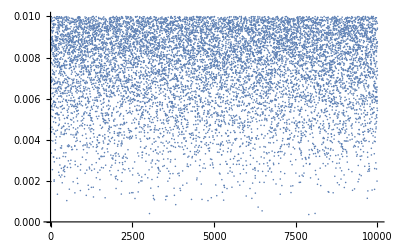
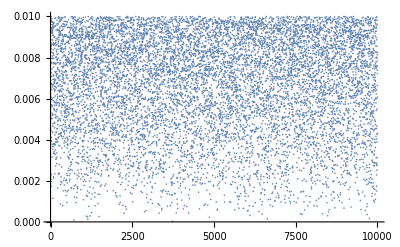
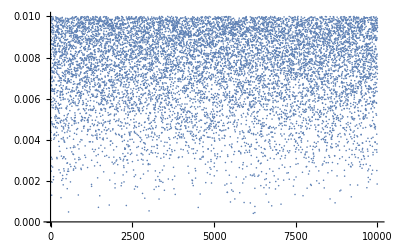
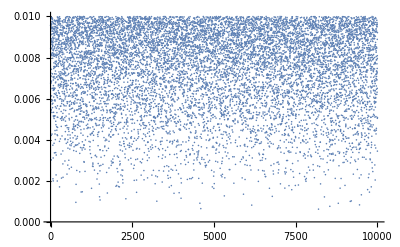
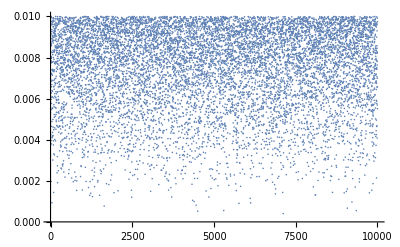
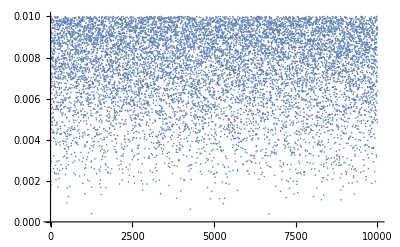
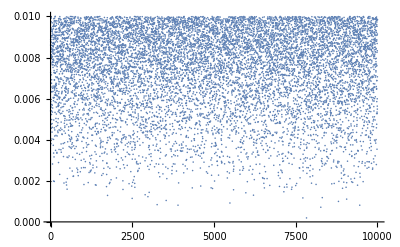
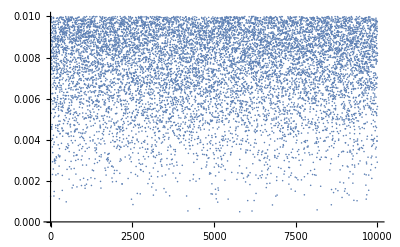
| p = 0.3 | p = 0.5 | p = 0.8
r_z = 0 | -Graphics- | -Graphics- | -Graphics-
r_z = 0.5 | -Graphics- | -Graphics- | -Graphics-
r_z = 0.8 | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{, Text["p = 0.3"], Text["p = 0.5"], Text["p = 0.8"]},
	  Join[{Text["r_z = 0"]}, errorPlotsR0allP],
	  Join[{Text["r_z = 0.5"]}, errorPlotsRp5allP], 
	  Join[{Text["r_z = 0.8"]}, errorPlotsRp8allP]
}]
```

```mathematica
Clear[brutalsR0allP, brutalsRp5allP, brutalsRp8allP]
Clear[errorsR0allP, errorsRp5allP, errorsRp8allP]
```

## Visualizaciones

```mathematica
(*importando preimágenes*)
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis"]
```

/media/storage/ciencia/investigacion/tesis

```mathematica
samplesR0 = ketsToDensity[Get["pureHaarStates_n=10000_p="<>ToString[#]<>"_rz=0.m"]]& /@ swapPs;
samplesRp5 = ketsToDensity[Get["pureHaarStates_n=10000_p="<>ToString[#]<>"_rz=0.5.m"]]& /@ swapPs;
samplesRp8 = ketsToDensity[Get["pureHaarStates_n=10000_p="<>ToString[#]<>"_rz=0.8.m"]]& /@ swapPs;
```

```mathematica
Outer[visualizeBipartiteSystem[#1[[1;;#2]]]&, samplesR0, {100, 1000, 10000}, 1]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
MapThread[Export["brutalRES_n="<>ToString[#2]<>"_p=0.8_rz=0.pdf", #1]&, {%28[[3]], {100, 1000, 10000}}]
```

{brutalRES_n=100_p=0.8_rz=0.pdf,brutalRES_n=1000_p=0.8_rz=0.pdf,brutalRES_n=10000_p=0.8_rz=0.pdf}

```mathematica
Outer[visualizeBipartiteSystem[#1[[1;;#2]]]&, samplesRp5, {100, 1000, 10000}, 1]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
MapThread[Export["brutalRES_n="<>ToString[#2]<>"_p=0.8_rz=0.5.pdf", #1]&, {%29[[3]], {100, 1000, 10000}}]
```

{brutalRES_n=100_p=0.8_rz=0.5.pdf,brutalRES_n=1000_p=0.8_rz=0.5.pdf,brutalRES_n=10000_p=0.8_rz=0.5.pdf}

```mathematica
Outer[visualizeBipartiteSystem[#1[[1;;#2]]]&, samplesRp8, {100, 1000, 10000}, 1]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
MapThread[Export["brutalRES_n="<>ToString[#2]<>"_p=0.8_rz=0.8.pdf", #1]&, {%30[[3]], {100, 1000, 10000}}]
```

{brutalRES_n=100_p=0.8_rz=0.8.pdf,brutalRES_n=1000_p=0.8_rz=0.8.pdf,brutalRES_n=10000_p=0.8_rz=0.8.pdf}

```mathematica
volBipartiteSubSpaceTarget[0.3, 0.]
```

281.989

```mathematica
volBipartiteSubSpaceTarget[0.2, 0.]
```

164.493

```mathematica
volBipartiteSubSpaceTarget[0.5, 0.]
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity